```mathematica
ops={not, or,xor,and, "=>", "<=>", NOR, NAND};
RandomChoice[ops, 20]
```

{=>,and,and,xor,NAND,NOR,NAND,NOR,xor,or,not,xor,xor,and,xor,xor,not,not,NAND,=>}

```mathematica
vars={x1, x2, x3};
RandomChoice[vars, 8]
```

{x2,x3,x2,x3,x1,x3,x1,x3}

```mathematica
expr=Xor[¬Nand[x1,x2]⧦x3,¬And[x2,x4]⇒Nor[x1,¬x3]]
Boole[BooleanTable[{x1, x2, x3, x4}->expr, {x1, x2, x3, x4}]]//TableForm
```

(x3⧦!(x1⊼x2))⊻(!(x2&&x4)⇒x1⊽!x3)

{True,True,True,True}→0
{True,True,True,False}→1
{True,True,False,True}→1
{True,True,False,False}→0
{True,False,True,True}→0
{True,False,True,False}→0
{True,False,False,True}→1
{True,False,False,False}→1
{False,True,True,True}→1
{False,True,True,False}→1
{False,True,False,True}→0
{False,True,False,False}→1
{False,False,True,True}→1
{False,False,True,False}→1
{False,False,False,True}→1
{False,False,False,False}→1

```mathematica
BooleanConvert[expr, "CNF"]
```

(!x1||!x2||x3||x4)&&(!x1||x2||!x3)&&(!x1||!x3||!x4)&&(x1||!x2||x3||!x4)

```mathematica
BooleanMinimize[expr]
```

(x1&&!x3&&x4)||(!x1&&x3)||(!x1&&!x4)||(x2&&x3&&!x4)||(!x2&&!x3)

```mathematica
table[f_]:=Boole[BooleanTable[{x1, x2, x3, x4}->f, {x1, x2, x3, x4}]]//TableForm
kek=table[expr]
```

{True,True,True,True}→Boole[expr]
{True,True,True,False}→Boole[expr]
{True,True,False,True}→Boole[expr]
{True,True,False,False}→Boole[expr]
{True,False,True,True}→Boole[expr]
{True,False,True,False}→Boole[expr]
{True,False,False,True}→Boole[expr]
{True,False,False,False}→Boole[expr]
{False,True,True,True}→Boole[expr]
{False,True,True,False}→Boole[expr]
{False,True,False,True}→Boole[expr]
{False,True,False,False}→Boole[expr]
{False,False,True,True}→Boole[expr]
{False,False,True,False}→Boole[expr]
{False,False,False,True}→Boole[expr]
{False,False,False,False}→Boole[expr]

```mathematica
1⊻(x4⊻x3⊻x3&&x4⊻x2⊻x2&&x3⊻x2&&x3&&x4⊻x1⊻x1&&x4⊻x1&&x2&&x4⊻x1&&x2&&x3)
BooleanMinimize[%, "ANF"]
If[kek==table[%], Print["Nice"], Print["Fail"]]
```

1⊻x1⊻x2⊻x3⊻x4⊻(x1&&x4)⊻(x2&&x3)⊻(x3&&x4)⊻(x1&&x2&&x3)⊻(x1&&x2&&x4)⊻(x2&&x3&&x4)

1⊻x1⊻x2⊻x3⊻x4⊻(x1&&x4)⊻(x2&&x3)⊻(x3&&x4)⊻(x1&&x2&&x3)⊻(x1&&x2&&x4)⊻(x2&&x3&&x4)

If[{True,True,True,True}→0
{True,True,True,False}→1
{True,True,False,True}→1
{True,True,False,False}→0
{True,False,True,True}→0
{True,False,True,False}→0
{True,False,False,True}→1
{True,False,False,False}→1
{False,True,True,True}→1
{False,True,True,False}→1
{False,True,False,True}→0
{False,True,False,False}→1
{False,False,True,True}→1
{False,False,True,False}→1
{False,False,False,True}→1
{False,False,False,False}→1=={True,True,True,True}→Boole[1]
{True,True,True,False}→Boole[!1]
{True,True,False,True}→Boole[!1]
{True,True,False,False}→Boole[1]
{True,False,True,True}→Boole[!1]
{True,False,True,False}→Boole[1]
{True,False,False,True}→Boole[!1]
{True,False,False,False}→Boole[!1]
{False,True,True,True}→Boole[1]
{False,True,True,False}→Boole[!1]
{False,True,False,True}→Boole[1]
{False,True,False,False}→Boole[!1]
{False,False,True,True}→Boole[!1]
{False,False,True,False}→Boole[!1]
{False,False,False,True}→Boole[!1]
{False,False,False,False}→Boole[1],Print[Nice],Print[Fail]]

```mathematica
Xor[Xor[x1&&Xor[x3, True]&&x4, True]&&Xor[Xor[x3,x1&&x3], True]&&Xor[!x1&&!x4, True]&&Xor[x2&&x3&&!x4, True]&&Xor[!x2&&!x3, True], True]
```

```mathematica
expr1=Nand[x1, x3]&&x2⧦Xor[x2, x3]
Boole[BooleanTable[{x1, x2, x3}->expr1, {x1, x2, x3}]]//TableForm
BooleanConvert[expr1, "CNF"]
```

(x1⊼x3)&&x2⧦x2⊻x3

{True,True,True}→1
{True,True,False}→1
{True,False,True}→0
{True,False,False}→1
{False,True,True}→0
{False,True,False}→1
{False,False,True}→0
{False,False,False}→1

(x1||!x3)&&(x2||!x3)

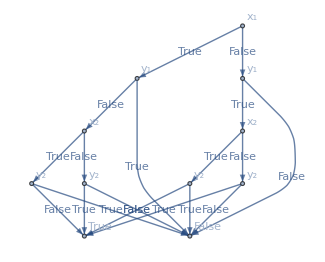

```mathematica
ClearAll[bddGraph];
bddGraph[bf_]:=With[{eq=Replace[BooleanConvert[bf,"IF"],If->List,∞,Heads->True]},Graph[(Labeled[#,Extract[eq,#~Append~1]]&/@Position[eq,_List])~Join~(Labeled[#,#]&/@{True,False}),Flatten[{Labeled[#->#~Append~2,True],Labeled[#->#~Append~3,False]}&/@Position[eq,_List],2]/.a_->b_:>a->Extract[eq,b]/;BooleanQ[Extract[eq,b]]]]
bddGraph[BooleanConvert[(Subscript[x, 1]⊻Subscript[y, 1])&&(Subscript[x, 2]⊻Subscript[y, 2]), "CNF"]]
```

```mathematica
Boole[BooleanTable[{p, q, r, s}->!(!p||r)&&(q||!r)&&(p⇒s), {p, q, r, s}]]//TableForm
```

{True,True,True,True}→0
{True,True,True,False}→0
{True,True,False,True}→1
{True,True,False,False}→0
{True,False,True,True}→0
{True,False,True,False}→0
{True,False,False,True}→1
{True,False,False,False}→0
{False,True,True,True}→0
{False,True,True,False}→0
{False,True,False,True}→0
{False,True,False,False}→0
{False,False,True,True}→0
{False,False,True,False}→0
{False,False,False,True}→0
{False,False,False,False}→0

```mathematica
BooleanMinimize[!(!p||r)&&(q||!r)&&(p⇒s)&&!s]
```

False

```mathematica
P[x_, y_]:=x==y
Q[x_, y_]:=x>y
ForAll[{x, y}, P[x, a]&&P[y, a]⇒Q[x, y]]
Resolve[%, Reals]
```

∀_{x,y}(x==a&&y==a⇒x>y)

False

```mathematica
g[x_]:=Sqrt[x]
Q[x_, y_]:=x==y
P[x_, y_]:=x==y
ForAll[{x, y}, Q[g[x], a]⇒P[x, y]]
Resolve[%, Reals]
```

∀_{x,y}(√x==a⇒x==y)

False

```mathematica
Boole[BooleanTable[{x, q0, q1, q2}->!x&&!q0&&!q1&&q2||x&&!q0&&q1&&!q2||x&&q0&&!q1&&!q2, {x, q0, q1, q2}]]//TableForm
```

{True,True,True,True}→0
{True,True,True,False}→0
{True,True,False,True}→0
{True,True,False,False}→1
{True,False,True,True}→0
{True,False,True,False}→1
{True,False,False,True}→0
{True,False,False,False}→0
{False,True,True,True}→0
{False,True,True,False}→0
{False,True,False,True}→0
{False,True,False,False}→0
{False,False,True,True}→0
{False,False,True,False}→0
{False,False,False,True}→1
{False,False,False,False}→0

```mathematica
BooleanConvert[x||y, "ANF"]
```

x⊻y⊻(x&&y)

```mathematica
BooleanMinimize[!a⊻c]
```

(a&&c)||(!a&&!c)

```mathematica
BooleanMinimize[((s⇒i)&&(i⇒g))⇒(s⇒g)]
```

True